Mathematica Appendix:

We first write the distance matrices for the two networks. For the Earth-Moon System, we have 9 nodes: 

(1) Earth
(2) Low Earth Orbit
(3) Moon Transfer Orbit
(4) Earth Escape/Capture
(5) Earth-Moon L1 (Lagrange point)
(6) Lunar Escape/Capture
(7) Earth-Moon L2 
(8) Low Lunar Orbit
(9) Moon.

					-Graphics-

```mathematica
ems={{0,9,12.12,12.21,12.7,12.26,12.47,12.94,14.66},{4.5,0,3.12,3.21,3.7,3.26,3.47,3.94,5.66},{6.06,1.56,0,0.09,0.58,0.14,0.35,0.82,2.54},{6.105,1.605,0.045,0,0.67,0.23,0.44,0.91,2.63},{6.64,2.14,0.58,0.67,0,0.72,0.93,0.64,2.36},{6.2,1.7,0.14,0.23,0.72,0,0.49,0.68,2.4},{6.41,1.91,0.35,0.44,0.93,0.49,0,0.64,2.36},{6.88,2.38,0.82,0.91,0.64,0.68,0.64,0,1.72},{8.6,4.1,2.54,2.63,2.36,2.4,2.36,1.72,0}};
MatrixForm[ems]
```

(0 | 9 | 12.12 | 12.21 | 12.7 | 12.26 | 12.47 | 12.94 | 14.66
4.5 | 0 | 3.12 | 3.21 | 3.7 | 3.26 | 3.47 | 3.94 | 5.66
6.06 | 1.56 | 0 | 0.09 | 0.58 | 0.14 | 0.35 | 0.82 | 2.54
6.105 | 1.605 | 0.045 | 0 | 0.67 | 0.23 | 0.44 | 0.91 | 2.63
6.64 | 2.14 | 0.58 | 0.67 | 0 | 0.72 | 0.93 | 0.64 | 2.36
6.2 | 1.7 | 0.14 | 0.23 | 0.72 | 0 | 0.49 | 0.68 | 2.4
6.41 | 1.91 | 0.35 | 0.44 | 0.93 | 0.49 | 0 | 0.64 | 2.36
6.88 | 2.38 | 0.82 | 0.91 | 0.64 | 0.68 | 0.64 | 0 | 1.72
8.6 | 4.1 | 2.54 | 2.63 | 2.36 | 2.4 | 2.36 | 1.72 | 0)

For the Earth-Moon-Mars System, we have 17 nodes: 

(1) Earth
(2) Low Earth Orbit
(3) Earth-Moon L4/5
(4) Geostationary Orbit (GEO)
(5) Geostationary Transfer Orbit (GTO)
(6) Low Lunar Orbit
(7) Moon
(8) Earth C3 = 0
(9) Mars Transfer Orbit
(10) Mars C3 = 0
(11) Deimos Transfer Orbit
(12) Deimos
(13) Phobos Transfer Orbit
(14) Phobos
(15) Low Mars Orbit
(16) Mars
(17)Sun.

					-Graphics-

```mathematica
emms={{0,9.5,13.6,13.3,12,13.4,15,12.7,13.3,13.75,13.85,14.55,14,14.5,14.45,16.5,39.5},
{4.75,0,4.1,3.8,2.5,3.9,5.5,3.2,3.8,4.25,4.35,5.05,4.5,5,4.95,7,30},
{6.8,2.05,0,1.7,1.75,0.7,2.3,1.4,2,2.45,2.55,3.25,2.7,3.2,3.15,5.2,32.05},
{6.65,1.9,1.7,0,1.6,2.4,4,2.3,2.9,3.35,3.45,4.15,3.6,4.1,4.05,6.1,31.9},
{6,1.25,3.3,1.6,0,1.4,3,0.7,1.3,1.75,1.85,2.55,2,2.5,2.45,4.5,31.25},
{7.05,2.3,0.7,2.4,1.05,0,1.6, 0.7,1.3,1.75,1.85,2.55,2,2.5,2.45,4.5,32.3},
{8.65,3.9,2.3,4,2.65,1.6,0,2.3,2.9,3.35,3.45,4.15,3.6,4.1,4.05,6.1,33.8},
{6.35,1.6,1.4,1.95,0.35,0.7,2.3,0,0.6,1.05,1.15,1.85,1.3,1.8,1.75,3.8,31.6},
{6.65,1.9,1.7,2.25,0.65,1,2.6,0.3,0,0.45,0.55,1.25,0.7,1.2,1.15,3.2,31.9},
{7.55,2.8,2.6,3.15,1.55,1.9,3.5,1.2,0.9,0,0.1,0.8,0.25,0.75,0.7,2.75,32.8},
{7.75,3,2.8,3.35,1.75,2.1,3.7,1.4,1.1,0.2,0,0.7,0.15,0.65,0.60,2.65,33},
{8.45,3.7,3.5,4.05,2.45,2.8,4.4,2.1,1.8,0.9,0.7,0,0.85,1.35,1.3,3.35,33.7},
{8.05,3.3,3.1,3.65,2.05,2.4,4,1.7,1.4,0.5,0.3,1,0,0.5,0.45,2.5,33.3},
{8.55,3.8,3.6,4.15,2.55,2.9,4.5,2.2,1.9,1,0.8,1.5,0.5,0,0.95,3,33.8},
{8.95,4.2,4,4.55,2.95,3.3,4.9,2.6,2.3,1.4,1.2,1.9,0.9,1.4,0,2.05,34.2},
{13.05,8.3,8.1,8.65,7.05,7.4,9,6.7,6.4,5.5,5.3,6,5,5.5,4.1,0,38.3},
{19.75,15,19.1,18.8,17.5,18.9,20.5,18.2,18.8,19.25,19.35,20.05,19.5,20,19.95,22,0}};
MatrixForm[emms]
```

(0 | 9.5 | 13.6 | 13.3 | 12 | 13.4 | 15 | 12.7 | 13.3 | 13.75 | 13.85 | 14.55 | 14 | 14.5 | 14.45 | 16.5 | 39.5
4.75 | 0 | 4.1 | 3.8 | 2.5 | 3.9 | 5.5 | 3.2 | 3.8 | 4.25 | 4.35 | 5.05 | 4.5 | 5 | 4.95 | 7 | 30
6.8 | 2.05 | 0 | 1.7 | 1.75 | 0.7 | 2.3 | 1.4 | 2 | 2.45 | 2.55 | 3.25 | 2.7 | 3.2 | 3.15 | 5.2 | 32.05
6.65 | 1.9 | 1.7 | 0 | 1.6 | 2.4 | 4 | 2.3 | 2.9 | 3.35 | 3.45 | 4.15 | 3.6 | 4.1 | 4.05 | 6.1 | 31.9
6 | 1.25 | 3.3 | 1.6 | 0 | 1.4 | 3 | 0.7 | 1.3 | 1.75 | 1.85 | 2.55 | 2 | 2.5 | 2.45 | 4.5 | 31.25
7.05 | 2.3 | 0.7 | 2.4 | 1.05 | 0 | 1.6 | 0.7 | 1.3 | 1.75 | 1.85 | 2.55 | 2 | 2.5 | 2.45 | 4.5 | 32.3
8.65 | 3.9 | 2.3 | 4 | 2.65 | 1.6 | 0 | 2.3 | 2.9 | 3.35 | 3.45 | 4.15 | 3.6 | 4.1 | 4.05 | 6.1 | 33.8
6.35 | 1.6 | 1.4 | 1.95 | 0.35 | 0.7 | 2.3 | 0 | 0.6 | 1.05 | 1.15 | 1.85 | 1.3 | 1.8 | 1.75 | 3.8 | 31.6
6.65 | 1.9 | 1.7 | 2.25 | 0.65 | 1 | 2.6 | 0.3 | 0 | 0.45 | 0.55 | 1.25 | 0.7 | 1.2 | 1.15 | 3.2 | 31.9
7.55 | 2.8 | 2.6 | 3.15 | 1.55 | 1.9 | 3.5 | 1.2 | 0.9 | 0 | 0.1 | 0.8 | 0.25 | 0.75 | 0.7 | 2.75 | 32.8
7.75 | 3 | 2.8 | 3.35 | 1.75 | 2.1 | 3.7 | 1.4 | 1.1 | 0.2 | 0 | 0.7 | 0.15 | 0.65 | 0.6 | 2.65 | 33
8.45 | 3.7 | 3.5 | 4.05 | 2.45 | 2.8 | 4.4 | 2.1 | 1.8 | 0.9 | 0.7 | 0 | 0.85 | 1.35 | 1.3 | 3.35 | 33.7
8.05 | 3.3 | 3.1 | 3.65 | 2.05 | 2.4 | 4 | 1.7 | 1.4 | 0.5 | 0.3 | 1 | 0 | 0.5 | 0.45 | 2.5 | 33.3
8.55 | 3.8 | 3.6 | 4.15 | 2.55 | 2.9 | 4.5 | 2.2 | 1.9 | 1 | 0.8 | 1.5 | 0.5 | 0 | 0.95 | 3 | 33.8
8.95 | 4.2 | 4 | 4.55 | 2.95 | 3.3 | 4.9 | 2.6 | 2.3 | 1.4 | 1.2 | 1.9 | 0.9 | 1.4 | 0 | 2.05 | 34.2
13.05 | 8.3 | 8.1 | 8.65 | 7.05 | 7.4 | 9 | 6.7 | 6.4 | 5.5 | 5.3 | 6 | 5 | 5.5 | 4.1 | 0 | 38.3
19.75 | 15 | 19.1 | 18.8 | 17.5 | 18.9 | 20.5 | 18.2 | 18.8 | 19.25 | 19.35 | 20.05 | 19.5 | 20 | 19.95 | 22 | 0)

Here we used the lowest delta-v path between every two nodes.

Next, we introduce commands for working with network adjacency matrices.

```mathematica
Init[Δ_,n_]:=Table[If[j==k,0,If[RandomReal[]<Δ,1,0]],{j,1,n},{k,1,n}]
RNSample[Δ_, n_,M_]:=Table[Init[Δ,n],{i, 1,M}]
Fd[x_]:=If[x==0,0,x^-b]
Unit[n_]:=Table[1,{j,1,n}]
```

We also introduce for-loops we use to concisely get the relative economic sizes of nodes in the networks.

```mathematica
High2[dist_,tops_,β_]:=For[i=1; Highest2list={},i<Length[tops]+1,i++,topdist=dist*tops[[i]];topdistb=Table[Map[Fd,topdist[[j]]],{j,1,Length[topdist]}];Evdist= Eigenvectors[topdistb/.b->β];
Evndist=Evdist[[1]]/Total[Evdist[[1]]];Highest2list=Append[Highest2list,Ordering[Evndist,-2]]]
```

```mathematica
FirstSec[Hi2_]:=For[i=1;FirstEv={};SecondEv={},i<Length[Hi2]+1,i++,FirstEv=Append[FirstEv,Hi2[[i]][[2]]];SecondEv=Append[SecondEv,Hi2[[i]][[1]]];]
```

Use this seed with commands involving random numbers to generate the same results every time:

```mathematica
SeedRandom[1234]
```

8.1 Analytical static solution: 

8.1.1 Earth-Moon System:

(a) Δ = .5, b = 1.5:

```mathematica
SeedRandom[1234];Sample1=RNSample[.5,9,10000];
```

```mathematica
High2[ems,Sample1,1.5]
```

Highest2list gives the 2 nodes with the largest relative economic volumes in equilibrium for each of the 10,000 networks in the sample.

```mathematica
FirstSec[Highest2list]
```

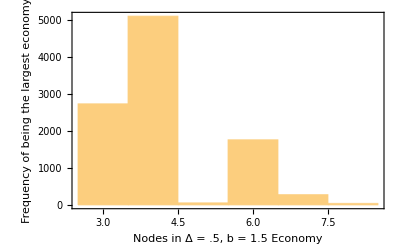

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 Economy","Frequency of being the largest economy"},PlotRange->Full]
```

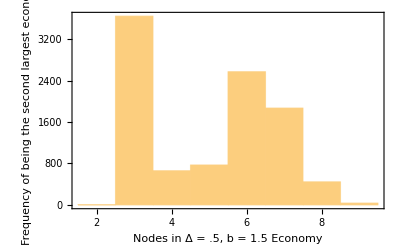

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 Economy","Frequency of being the second largest economy"},PlotRange->Full]
```

Let us pick a random network from the sample of 10,000 to visualize its equilibrium relative economic volumes.

```mathematica
RandNetwork = Sample1[[RandomInteger[{1,10000}]]];
MatrixForm[RandNetwork]
```

(0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0)

```mathematica
DRand = ems*RandNetwork;
DRandB=Table[Map[Fd,DRand[[j]]],{j,1,Length[DRand]}];
MatrixForm[DRandB]
```

(0 | 0 | 12.12^-b | 12.21^-b | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.12^-b | 0 | 3.7^-b | 0 | 3.47^-b | 3.94^-b | 5.66^-b
0 | 0 | 0 | 0 | 0 | 0.14^-b | 0.35^-b | 0 | 0
6.105^-b | 1.605^-b | 0 | 0 | 0 | 0.23^-b | 0 | 0.91^-b | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.64^-b | 0
0 | 1.7^-b | 0 | 0.23^-b | 0 | 0 | 0 | 0 | 2.4^-b
0 | 0 | 0.35^-b | 0 | 0 | 0 | 0 | 0 | 2.36^-b
6.88^-b | 0 | 0.82^-b | 0 | 0.64^-b | 0.68^-b | 0 | 0 | 0
0 | 0 | 2.54^-b | 2.63^-b | 0 | 2.4^-b | 2.36^-b | 0 | 0)

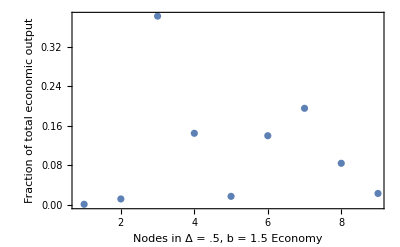

```mathematica
Ev1=Eigenvectors[DRandB/.b->1.5];
Evn1=Ev1[[1]]/Total[Ev1[[1]]]//N;
ListPlot[Evn1,Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 Economy","Fraction of total economic output"},PlotRange->Full]
```

In this instance, nodes 3 (Moon Transfer Orbit) and 7 (Earth-Moon L2) account for nearly 60% of the total economic output.

Now we can limit the analysis to the networks in the sample where the in-degree of Earth is at least Δ(n-1) (= 4 in this case) with the following loop:

```mathematica
LimReal[tops_,thresh_,n_]:=For[i=1;RealSample={},i<Length[tops]+1,i++,If[(Unit[n].tops[[i]])[[1]]⩾thresh,RealSample=Append[RealSample,tops[[i]]],Continue[]]]
```

```mathematica
LimReal[Sample1,4,9]
```

```mathematica
Length[RealSample]
```

6353

In this sample, roughly 64% of the networks fit our “realistic” criterion.

```mathematica
High2[ems,RealSample,1.5]
```

```mathematica
FirstSec[Highest2list]
```

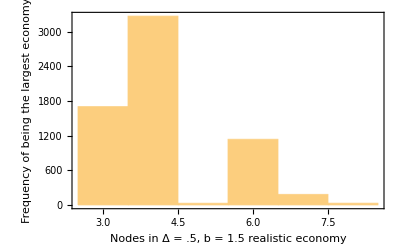

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

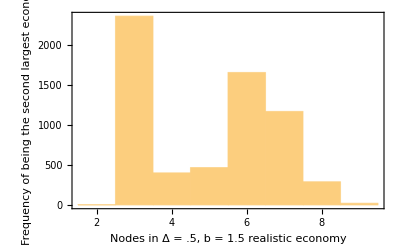

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

(b) Δ = .5, b = 2: (keep the same sample to isolate the effect of changing b)

```mathematica
High2[ems,Sample1,2]
```

```mathematica
FirstSec[Highest2list]
```

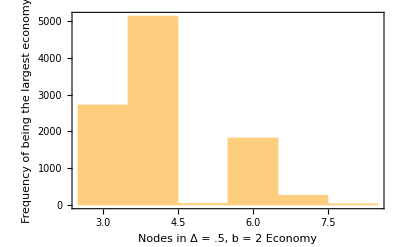

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 Economy","Frequency of being the largest economy"},PlotRange->Full]
```

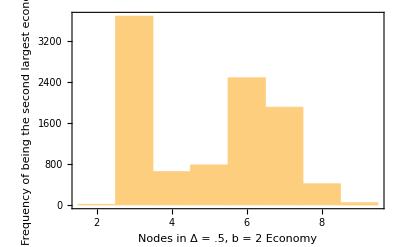

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 Economy","Frequency of being the second largest economy"},PlotRange->Full]
```

```mathematica
High2[ems,RealSample,2]
```

```mathematica
FirstSec[Highest2list]
```

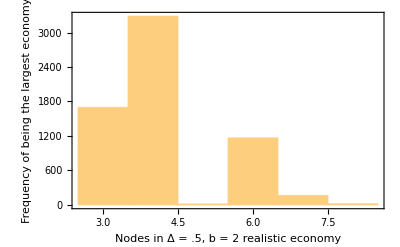

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

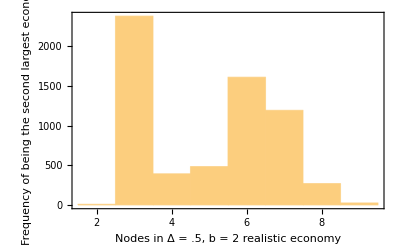

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

(c) Δ = .6, b = 1.5:

```mathematica
SeedRandom[1234];Sample2=RNSample[.6,9,10000];
```

```mathematica
High2[ems,Sample2,1.5]
```

```mathematica
FirstSec[Highest2list]
```

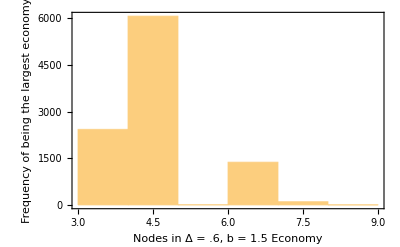

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 Economy","Frequency of being the largest economy"},PlotRange->Full]
```

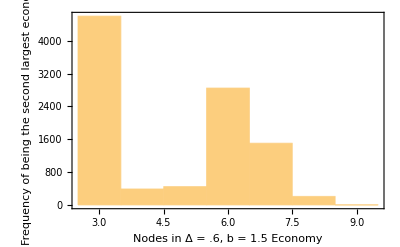

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 Economy","Frequency of being the second largest economy"},PlotRange->Full]
```

The realistic threshold is now Δ(n-1) = 4.8, so effectively 5.

```mathematica
LimReal[Sample2,5,9]
```

```mathematica
Length[RealSample]
```

6016

The proportion of realistic networks is about 60%.

```mathematica
High2[ems,RealSample,1.5]
```

```mathematica
FirstSec[Highest2list]
```

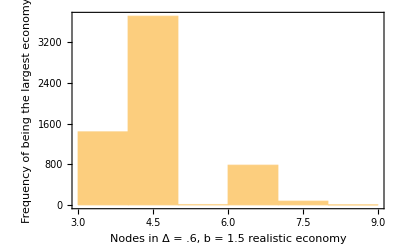

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

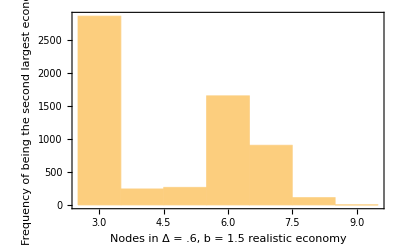

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

(d) Δ = .6, b = 2:

```mathematica
High2[ems,Sample2,2]
```

```mathematica
FirstSec[Highest2list]
```

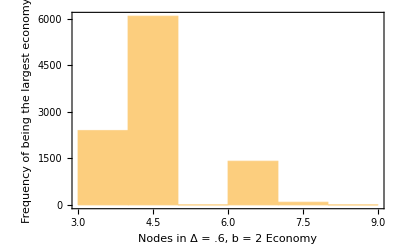

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 Economy","Frequency of being the largest economy"},PlotRange->Full]
```

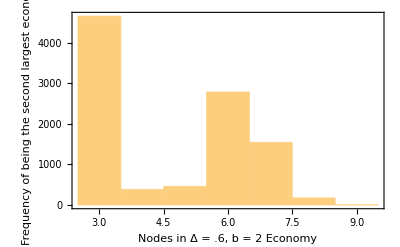

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 Economy","Frequency of being the second largest economy"},PlotRange->Full]
```

```mathematica
High2[ems,RealSample,2]
```

```mathematica
FirstSec[Highest2list]
```

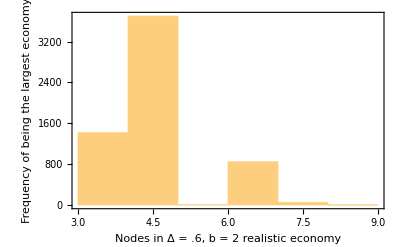

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

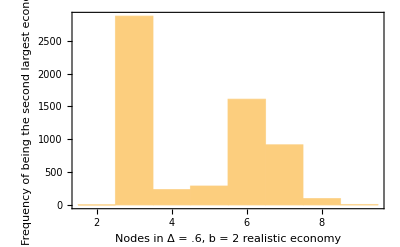

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

8.1.2 Earth-Moon-Mars System:

(a) Δ = .5, b = 1.5:

```mathematica
SeedRandom[1234];Sample3=RNSample[.5,17,10000];
```

```mathematica
High2[emms,Sample3,1.5]
```

```mathematica
FirstSec[Highest2list]
```

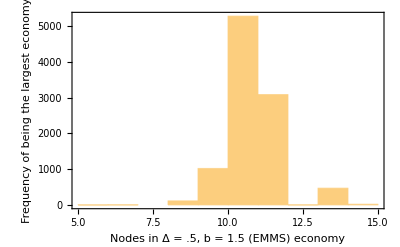

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 (EMMS) economy","Frequency of being the largest economy"},PlotRange->Full]
```

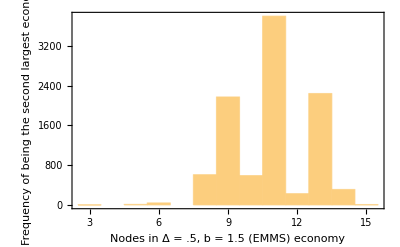

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 (EMMS) economy","Frequency of being the second largest economy"},PlotRange->Full]
```

The realistic threshold is Δ(n-1) = 8.

```mathematica
LimReal[Sample3,8,17]
```

```mathematica
Length[RealSample]
```

5950

About 60% of the networks in the sample are realistic.

```mathematica
High2[emms,RealSample,1.5]
```

```mathematica
FirstSec[Highest2list]
```

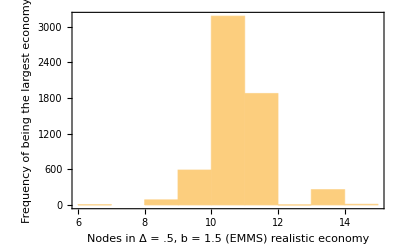

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 (EMMS) realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

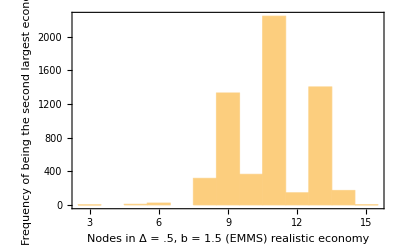

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 1.5 (EMMS) realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

(b) Δ = .5, b = 2:

```mathematica
High2[emms,Sample3,2]
```

```mathematica
FirstSec[Highest2list]
```

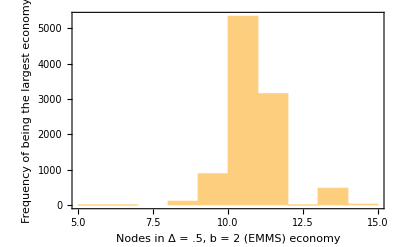

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 (EMMS) economy","Frequency of being the largest economy"},PlotRange->Full]
```

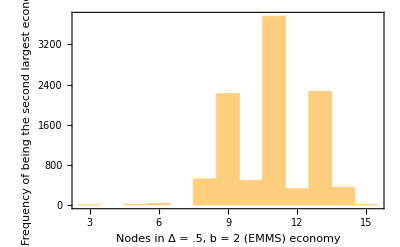

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 (EMMS) economy","Frequency of being the second largest economy"},PlotRange->Full]
```

```mathematica
High2[emms,RealSample,2]
```

```mathematica
FirstSec[Highest2list]
```

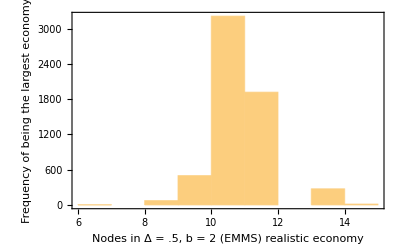

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 (EMMS) realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

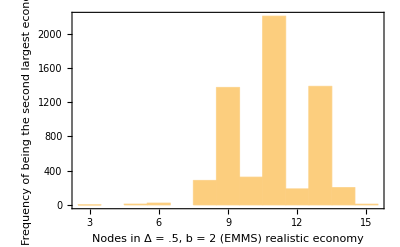

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .5, b = 2 (EMMS) realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

(c) Δ = .6, b = 1.5:

```mathematica
SeedRandom[1234];Sample4=RNSample[.6,17,10000];
```

```mathematica
High2[emms,Sample4,1.5]
```

```mathematica
FirstSec[Highest2list]
```

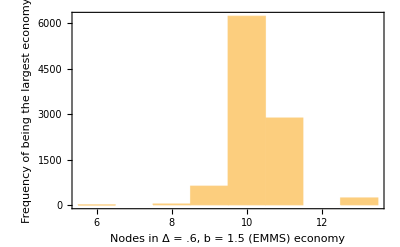

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 (EMMS) economy","Frequency of being the largest economy"},PlotRange->Full]
```

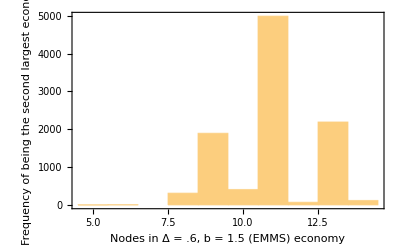

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 (EMMS) economy","Frequency of being the second largest economy"},PlotRange->Full]
```

The realistic threshold is now Δ(n-1) = 9.6, so effectively 10.

```mathematica
LimReal[Sample4,10,17]
```

```mathematica
Length[RealSample]
```

5259

Now only around 53% of networks are realistic.

```mathematica
High2[emms,RealSample,1.5]
```

```mathematica
FirstSec[Highest2list]
```

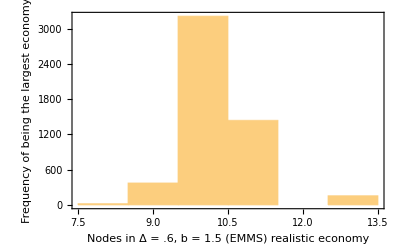

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 (EMMS) realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

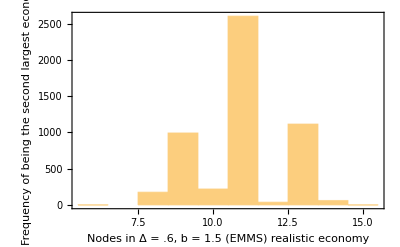

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 1.5 (EMMS) realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

(d) Δ = .6, b = 2:

```mathematica
High2[emms,Sample4,2]
```

```mathematica
FirstSec[Highest2list]
```

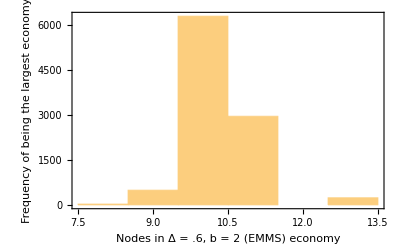

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 (EMMS) economy","Frequency of being the largest economy"},PlotRange->Full]
```

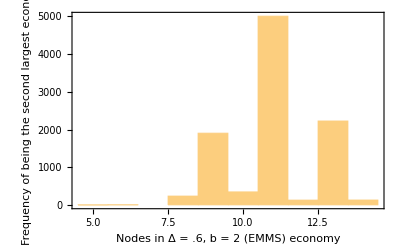

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 (EMMS) economy","Frequency of being the second largest economy"},PlotRange->Full]
```

Let us pick a random network from the sample of 10,000 to visualize its relative economic volumes.

```mathematica
RandNetwork2 = Sample4[[RandomInteger[{1,10000}]]];
MatrixForm[RandNetwork2]
```

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

```mathematica
DRand2 = emms*RandNetwork2;
DRandB2=Table[Map[Fd,DRand2[[j]]],{j,1,Length[DRand2]}];
MatrixForm[DRandB2]
```

(0 | 9.5^-b | 0 | 13.3^-b | 0 | 0 | 0 | 12.7^-b | 13.3^-b | 13.75^-b | 13.85^-b | 14.55^-b | 14^-b | 14.5^-b | 0 | 0 | 39.5^-b
4.75^-b | 0 | 4.1^-b | 3.8^-b | 2.5^-b | 0 | 0 | 0 | 3.8^-b | 0 | 4.35^-b | 0 | 0 | 5^-b | 4.95^-b | 0 | 30^-b
6.8^-b | 2.05^-b | 0 | 1.7^-b | 0 | 0.7^-b | 0 | 1.4^-b | 2^-b | 0 | 2.55^-b | 3.25^-b | 0 | 3.2^-b | 3.15^-b | 5.2^-b | 0
6.65^-b | 1.9^-b | 1.7^-b | 0 | 0 | 0 | 4^-b | 0 | 2.9^-b | 3.35^-b | 0 | 4.15^-b | 0 | 4.1^-b | 0 | 0 | 0
0 | 0 | 3.3^-b | 1.6^-b | 0 | 1.4^-b | 0 | 0.7^-b | 0 | 1.75^-b | 1.85^-b | 2.55^-b | 2^-b | 2.5^-b | 2.45^-b | 4.5^-b | 31.25^-b
7.05^-b | 0 | 0.7^-b | 2.4^-b | 1.05^-b | 0 | 0 | 0.7^-b | 1.3^-b | 0 | 0 | 2.55^-b | 2^-b | 2.5^-b | 0 | 4.5^-b | 32.3^-b
0 | 3.9^-b | 2.3^-b | 0 | 2.65^-b | 1.6^-b | 0 | 2.3^-b | 2.9^-b | 3.35^-b | 0 | 4.15^-b | 0 | 0 | 0 | 6.1^-b | 0
6.35^-b | 0 | 0 | 1.95^-b | 0 | 0.7^-b | 2.3^-b | 0 | 0 | 1.05^-b | 0 | 1.85^-b | 0 | 0 | 0 | 0 | 0
0 | 1.9^-b | 0 | 2.25^-b | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.7^-b | 1.2^-b | 1.15^-b | 0 | 31.9^-b
7.55^-b | 2.8^-b | 0 | 3.15^-b | 1.55^-b | 0 | 3.5^-b | 1.2^-b | 0.9^-b | 0 | 0.1^-b | 0 | 0 | 0.75^-b | 0 | 0 | 32.8^-b
7.75^-b | 0 | 2.8^-b | 0 | 1.75^-b | 0 | 3.7^-b | 0 | 1.1^-b | 0 | 0 | 0.7^-b | 0 | 0 | 0.6^-b | 0 | 33^-b
0 | 0 | 3.5^-b | 0 | 2.45^-b | 2.8^-b | 4.4^-b | 2.1^-b | 1.8^-b | 0.9^-b | 0.7^-b | 0 | 0 | 1.35^-b | 1.3^-b | 3.35^-b | 0
8.05^-b | 0 | 3.1^-b | 3.65^-b | 0 | 0 | 4^-b | 0 | 1.4^-b | 0.5^-b | 0 | 0 | 0 | 0 | 0.45^-b | 2.5^-b | 33.3^-b
0 | 3.8^-b | 0 | 0 | 2.55^-b | 2.9^-b | 0 | 2.2^-b | 1.9^-b | 1 | 0 | 1.5^-b | 0.5^-b | 0 | 0.95^-b | 0 | 33.8^-b
8.95^-b | 4.2^-b | 0 | 0 | 2.95^-b | 3.3^-b | 0 | 0 | 0 | 0 | 1.2^-b | 0 | 0.9^-b | 1.4^-b | 0 | 0 | 0
0 | 8.3^-b | 0 | 0 | 0 | 7.4^-b | 9^-b | 6.7^-b | 6.4^-b | 5.5^-b | 5.3^-b | 6^-b | 0 | 0 | 4.1^-b | 0 | 38.3^-b
19.75^-b | 15^-b | 0 | 18.8^-b | 0 | 0 | 20.5^-b | 18.2^-b | 18.8^-b | 0 | 0 | 0 | 0 | 20^-b | 0 | 22^-b | 0)

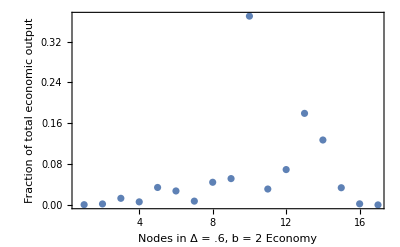

```mathematica
Ev2=Eigenvectors[DRandB2/.b->2];
Evn2=Ev2[[1]]/Total[Ev2[[1]]]//N;
ListPlot[Evn2,Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 Economy","Fraction of total economic output"},PlotRange->Full]
```

In this case, nodes 10 (Mars C3 = 0) and 13 (Phobos Transfer) account for almost 60% of total economic output.

```mathematica
High2[emms,RealSample,2]
```

```mathematica
FirstSec[Highest2list]
```

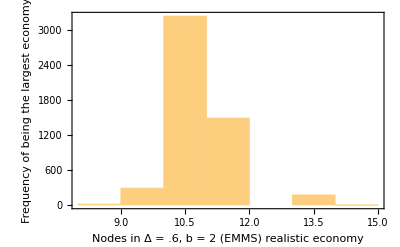

```mathematica
Histogram[FirstEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 (EMMS) realistic economy","Frequency of being the largest economy"},PlotRange->Full]
```

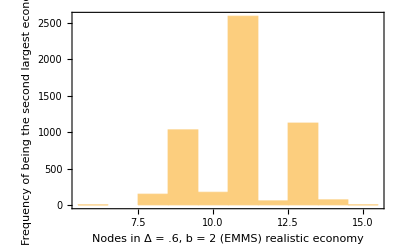

```mathematica
Histogram[SecondEv, Frame->True,FrameLabel->{"Nodes in Δ = .6, b = 2 (EMMS) realistic economy","Frequency of being the second largest economy"},PlotRange->Full]
```

Now we carry out the iterative gravity solution for each system. Below are the functions which we will use for initializing economic volumes and updating the topology of the network.

```mathematica
InitVolumes[n_]:=For[i=0;InitVolumesList={RandomReal[{90,110}]},i<n-1,i++,InitVolumesList=Append[InitVolumesList,RandomReal[{10,30}]]]
```

```mathematica
TradeLinks[n_,z_,τ_,distm_,vols_]:=Table[If[j==k,0,(z*vols[[j]]*vols[[k]]*ⅇ^(-τ*distm[[j,k]]))/(1+z*vols[[j]]*vols[[k]]*ⅇ^(-τ*distm[[j,k]]))],{j,1,n},{k,1,n}]
```

```mathematica
RealizedLinks[n_,TradeLinksIt_]:=Table[If[RandomReal[]<TradeLinksIt[[j,k]],1,0],{j,1,n},{k,1,n}]
```

```mathematica
UpdateTopology[n_,z_,τ_,distm_,vols_]:=Do[TradeLinksIt=TradeLinks[n,z,τ,distm,vols];RealizedLinksIt=RealizedLinks[n,TradeLinksIt];topm=RealizedLinksIt*distm;wtopm=Table[Map[Fd,topm[[j]]],{j,1,Length[topm]}]/.b->1.5;,1]
```

And now the commands for updating economic volumes through marginal trade flows.

```mathematica
CalcMargin[n_,vols_,top_]:=For[i=1;MarginList={},i<n+1,i++,Mflowsi=vols*top[[i]];MarginList=Append[MarginList,Total[Mflowsi]]]
```

```mathematica
EconomicGrowth[n_,top_]:=Do[CalcMargin[n,WorkingVols,top];WorkingVols=WorkingVols+MarginList,5]
```

8.2 Iterative gravity solution:

Each network will be taken through 15 stages of growth, and thus 2 topology updates after the initial topology.

8.2.1 Earth-Moon System:

(a) z = .1, τ = 1:

```mathematica
InitVolumes[9]
```

```mathematica
InitVolumesList
```

{92.7218,22.7479,16.4933,21.651,24.2984,20.7965,13.6409,28.4692,21.9694}

Earth has by far the highest economic volume to begin with, as intended. We determine the topology based on these volumes:

```mathematica
UpdateTopology[9,.1,1,ems,InitVolumesList]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.104757 | 0 | 0.181455 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0
0 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0 | 0 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

Notice that this network is more connected than the ITN around the middle nodes and less connected for Earth, which has the highest delta-v’s to its neighbors. Now we go through 5 periods of economic growth.

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
WorkingVols
```

{92.7218,8.59134×10^7,3.3926×10^10,5.21618×10^10,3.03795×10^9,1.6467×10^10,5.76159×10^9,2.20922×10^9,4.12696×10^8}

Earth hasn’t grown at all, whereas nodes 4 and 3 have already become the the economic centers of the network. Now we update the topology based on these volumes:

```mathematica
UpdateTopology[9,.1,1,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0.0227091 | 0.0214832 | 0.0178155
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0.0396508 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

We have a fully connected network for these parameters after 5 periods of growth because of the high economic volumes in relation to delta-v values. We go through 5 more stages of growth:

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
WorkingVols
```

{6.65136×10^16,4.89055×10^17,5.70956×10^19,9.21333×10^19,5.21763×10^18,2.84623×10^19,9.90646×10^18,3.79473×10^18,7.08469×10^17}

The ordering of economic centers has been preserved even with a complete network. As economic volumes  weakly increase with each step, any future network update will also result in a complete network. We update the topology once again and go through 5 more periods of economic growth.

```mathematica
UpdateTopology[9,.1,1,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0.0227091 | 0.0214832 | 0.0178155
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0.0396508 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
WorkingVols
```

{1.14915×10^26,8.44868×10^26,9.95959×10^28,1.56731×10^29,9.00658×10^27,4.89631×10^28,1.70894×10^28,6.55074×10^27,1.22361×10^27}

We now compare the relative economic sizes of the nodes.

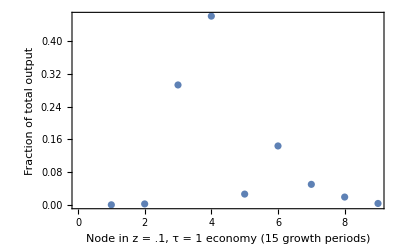

```mathematica
RV1=WorkingVols/Total[WorkingVols];
ListPlot[RV1, Frame->True,FrameLabel->{"Node in z = .1, τ = 1 economy (15 growth periods)","Fraction of total output"}]
```

Nodes 4, 3, and (to a lesser extent) 6 dominate, just like in the result for the static solution.

(b) z = .03, τ = 1:

Now we simulate with a lower value of z, which should make the initial network scarcer.

```mathematica
UpdateTopology[9,.03,1,ems,InitVolumesList];
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.173877 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 37.037 | 0 | 19.0901 | 4.82945 | 1.34673 | 0
0 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0 | 0 | 2.2639 | 0 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0
0 | 0.378835 | 0 | 0 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The initial network is more scarce than for z = .1, as expected.

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
WorkingVols
```

{92.7218,1.26433×10^8,3.13004×10^10,4.97507×10^10,1.46221×10^9,1.53848×10^10,7.32604×10^8,1.91263×10^9,21.9694}

Now we update the topology with these volumes:

```mathematica
UpdateTopology[9,.03,1,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0.0227091 | 0.0214832 | 0
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

We have a fully-connected network except that Earth and the Moon don’t trade with each other. We go through the next 5 stages of growth.

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
WorkingVols
```

{6.16646×10^16,4.54627×10^17,5.33567×10^19,8.49369×10^19,4.84824×10^18,2.63982×10^19,9.20193×10^18,3.52618×10^18,6.58469×10^17}

Now we update the topology for the second time.

```mathematica
UpdateTopology[9,.03,1,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0.0227091 | 0.0214832 | 0.0178155
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0.0396508 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

Now we have a fully connected network. We go through the 5 final stages of growth and compare relative economic volumes.

```mathematica
EconomicGrowth[9,wtopm]
```

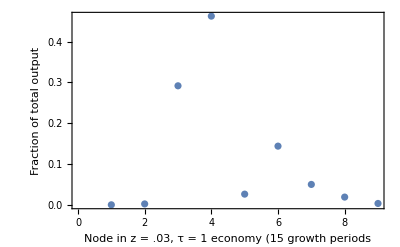

```mathematica
RV2=WorkingVols/Total[WorkingVols];
ListPlot[RV2, Frame->True,FrameLabel->{"Node in z = .03, τ = 1 economy (15 growth periods","Fraction of total output"}]
```

This picture is virtually identical to where z = .03. 

(c) z = .1, τ = 2:

This choice of parameters has delta-V be a more important factor in establishing the topology of the network.

```mathematica
UpdateTopology[9,.1,2,ems,InitVolumesList];
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.181455 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 37.037 | 2.2639 | 19.0901 | 0 | 1.34673 | 0
0 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 0 | 1.15196 | 0
0 | 0 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0 | 0.451156 | 0 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0
0 | 0.378835 | 4.82945 | 3.42627 | 0 | 2.91545 | 0 | 1.95313 | 0
0 | 0 | 1.34673 | 1.15196 | 0 | 1.78335 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.275824 | 0 | 0 | 0.44331 | 0)

Accordingly, we have heavy connectivity in the middle nodes and poor connectivity for the connections with high delta-V’s.

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
UpdateTopology[9,.1,2,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0 | 0 | 0
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0.0396508 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

The matrix is nearly fully connected (Earth is missing 3 export relationships).

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
UpdateTopology[9,.1,2,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0.0227091 | 0.0214832 | 0.0178155
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0.0396508 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

We once again have a fully connected network after 10 periods. We go through the final 5 stages of economic growth and compare relative economic sizes.

```mathematica
EconomicGrowth[9, wtopm]
```

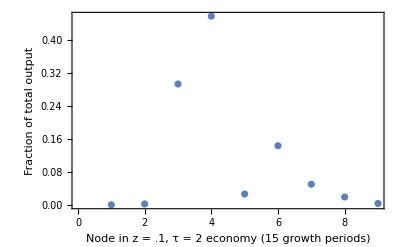

```mathematica
RV3=WorkingVols/Total[WorkingVols];
ListPlot[RV3, Frame->True,FrameLabel->{"Node in z = .1, τ = 2 economy (15 growth periods)","Fraction of total output"}]
```

The relative weights of the economies look the same as for (a) and (b).

(d) z = .03, τ = 2:

```mathematica
UpdateTopology[9,.03,2,ems,InitVolumesList]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0
0 | 0.491799 | 104.757 | 0 | 0 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0 | 0 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0
0 | 0.451156 | 0 | 9.06584 | 0 | 0 | 2.91545 | 1.78335 | 0
0 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 0 | 0 | 1.95313 | 0
0 | 0 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.44331 | 0)

As expected, this network is initially the scarcest we see.

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
UpdateTopology[9,.03,2,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0.0236999 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

Once again we don’t have a fully connected network after 5 periods of economic growth mainly due to missing export relationships for Earth.

```mathematica
EconomicGrowth[9,wtopm]
```

```mathematica
UpdateTopology[9,.03,2,ems,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.037037 | 0.0236999 | 0.0234383 | 0.022095 | 0.0232951 | 0.0227091 | 0.0214832 | 0.0178155
0.104757 | 0 | 0.181455 | 0.173877 | 0.140507 | 0.169892 | 0.154706 | 0.127866 | 0.0742635
0.0670334 | 0.513231 | 0 | 37.037 | 2.2639 | 19.0901 | 4.82945 | 1.34673 | 0.24703
0.0662936 | 0.491799 | 104.757 | 0 | 1.82342 | 9.06584 | 3.42627 | 1.15196 | 0.234459
0.0584451 | 0.319433 | 2.2639 | 1.82342 | 0 | 1.63682 | 1.115 | 1.95313 | 0.275824
0.0647758 | 0.451156 | 19.0901 | 9.06584 | 1.63682 | 0 | 2.91545 | 1.78335 | 0.268957
0.0616188 | 0.378835 | 4.82945 | 3.42627 | 1.115 | 2.91545 | 0 | 1.95313 | 0.275824
0.0554137 | 0.272355 | 1.34673 | 1.15196 | 1.95313 | 1.78335 | 1.95313 | 0 | 0.44331
0.0396508 | 0.120455 | 0.24703 | 0.234459 | 0.275824 | 0.268957 | 0.275824 | 0.44331 | 0)

We once again have a fully connected network after 10 periods.

```mathematica
EconomicGrowth[9, wtopm]
```

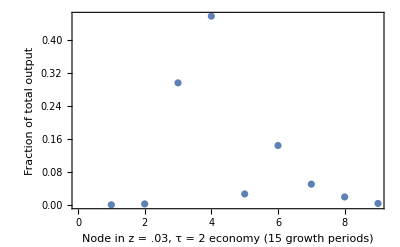

```mathematica
RV4=WorkingVols/Total[WorkingVols];
ListPlot[RV4, Frame->True,FrameLabel->{"Node in z = .03, τ = 2 economy (15 growth periods)","Fraction of total output"}]
```

We arrive at the same picture about the relative sizes of the nodes in the network as with the other parameter combinations. We can combine all final graphs to visualize the overlap in results:

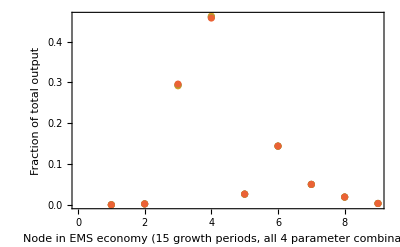

```mathematica
ListPlot[{RV1,RV2,RV3,RV4}, Frame->True,FrameLabel->{"Node in EMS economy (15 growth periods, all 4 parameter combinations)","Fraction of total output"}]
```

8.2.2 Earth-Moon-Mars System:

(a) z = .1, τ = 1:

```mathematica
InitVolumes[17]
```

```mathematica
InitVolumesList
```

{95.6294,16.685,19.0525,27.703,20.0467,20.5284,12.3049,18.1669,13.1928,20.1182,10.9233,15.9903,22.8303,28.103,15.977,29.8378,18.9216}

```mathematica
UpdateTopology[17,.1,1,emms,InitVolumesList]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0965961 | 0 | 0 | 0 | 0.252982 | 0 | 0 | 0.174693 | 0.134997 | 0.114134 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.340698 | 0 | 0 | 0.431959 | 1.70747 | 0 | 0.603682 | 0.353553 | 0.260766 | 0 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0 | 0
0 | 0.38183 | 0.451156 | 0 | 0.494106 | 0 | 0 | 0.286687 | 0.20249 | 0 | 0 | 0 | 0.146402 | 0 | 0 | 0 | 0
0.0680414 | 0.715542 | 0 | 0.494106 | 0 | 0.603682 | 0.19245 | 0 | 0 | 0.431959 | 0.397413 | 0.245578 | 0 | 0.252982 | 0 | 0.104757 | 0
0 | 0.286687 | 1.70747 | 0.268957 | 0 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0 | 0
0 | 0.129838 | 0.286687 | 0 | 0.231809 | 0.494106 | 0 | 0.286687 | 0 | 0 | 0.156053 | 0.118285 | 0 | 0 | 0 | 0 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0 | 0.431959 | 0 | 0
0 | 0.38183 | 0.451156 | 0 | 1.90823 | 1 | 0 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0 | 0
0 | 0 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0 | 0
0 | 0.19245 | 0.213434 | 0.163092 | 0 | 0.328603 | 0 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0 | 0 | 0 | 0.122692 | 0.260766 | 0.213434 | 0 | 0.328603 | 0 | 0 | 1.70747 | 0 | 1.27606 | 0.637528 | 0 | 0.163092 | 0
0 | 0.166813 | 0 | 0 | 0 | 0.268957 | 0.125 | 0.451156 | 0 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0 | 0.134997 | 0 | 0.118285 | 0.245578 | 0.20249 | 0 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0 | 0 | 0.125 | 0 | 0.197364 | 0 | 0 | 0.238528 | 0.286687 | 0 | 0.760726 | 0.38183 | 0 | 0.603682 | 0 | 0.340698 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0775275 | 0 | 0 | 0 | 0.0775275 | 0.120455 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[17,wtopm]
```

Let’s see the relative sizes of the nodes after 5 periods of growth under the initial topology.

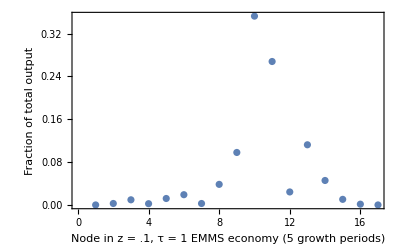

```mathematica
RV5a=WorkingVols/Total[WorkingVols];
ListPlot[RV5a, Frame->True,FrameLabel->{"Node in z = .1, τ = 1 EMMS economy (5 growth periods)","Fraction of total output"}]
```

Nodes 10, 11, and to a lesser extent 13 (and 9) dominate. This is already consistent with the results from the static solution.

```mathematica
UpdateTopology[17,.1,1,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.0341519 | 0.0199385 | 0.0206169 | 0.0240563 | 0.0203865 | 0.0172133 | 0.022095 | 0.0206169 | 0.0196131 | 0.0194011 | 0.018018 | 0.0190901 | 0.0181112 | 0.0182053 | 0 | 0
0.0965961 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0.0539949 | 0
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0393075 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0
0.0212121 | 0.0418199 | 0.0433783 | 0.0393075 | 0.0534215 | 0.0496767 | 0.037037 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0
0 | 0.0172133 | 0 | 0 | 0 | 0.0121705 | 0 | 0.0128793 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

We have a very nearly connected network. Here, the Sun is the most disconnected node (as expected).

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.1,1,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.0341519 | 0.0199385 | 0.0206169 | 0.0240563 | 0.0203865 | 0.0172133 | 0.022095 | 0.0206169 | 0.0196131 | 0.0194011 | 0.018018 | 0.0190901 | 0.0181112 | 0.0182053 | 0.0149202 | 0.00402814
0.0965961 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0.0539949 | 0.00608581
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0.00551135
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0.00555027
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0.00572433
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0.00544749
0.0393075 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0.00508891
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0.00562949
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0.00555027
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0.0053234
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0.00527508
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0.00511158
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0.00520396
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0.00508891
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0.00499989
0.0212121 | 0.0418199 | 0.0433783 | 0.0393075 | 0.0534215 | 0.0496767 | 0.037037 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0.00421893
0.0113933 | 0.0172133 | 0.0119798 | 0.0122677 | 0.0136598 | 0.0121705 | 0.0107738 | 0.0128793 | 0.0122677 | 0.0118401 | 0.0117484 | 0.0111385 | 0.0116131 | 0.0111803 | 0.0112224 | 0.00969094 | 0)

After 10 periods, we have a fully connected network.

```mathematica
EconomicGrowth[17,wtopm]
```

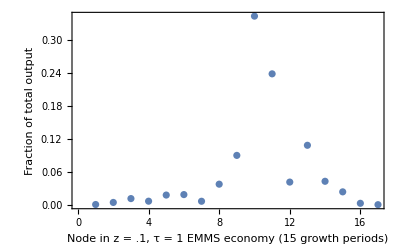

```mathematica
RV5=WorkingVols/Total[WorkingVols];
ListPlot[RV5, Frame->True,FrameLabel->{"Node in z = .1, τ = 1 EMMS economy (15 growth periods)","Fraction of total output"}]
```

The ordering of economic centers is largely preserved compared to 10 periods before. 

(b) z = .03, τ = 1:

```mathematica
UpdateTopology[17,.03,1,emms,InitVolumesList]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.252982 | 0.129838 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0 | 0.603682 | 0 | 0.260766 | 0.245578 | 0.170677 | 0 | 0 | 0 | 0 | 0
0 | 0.38183 | 0.451156 | 0 | 0 | 0.268957 | 0 | 0.286687 | 0.20249 | 0 | 0 | 0.118285 | 0 | 0 | 0 | 0 | 0
0 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0 | 0 | 0.67466 | 0.431959 | 0.397413 | 0 | 0.353553 | 0.252982 | 0 | 0 | 0
0 | 0.286687 | 0 | 0 | 0.929429 | 0 | 0 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0 | 0 | 0
0 | 0.129838 | 0 | 0.125 | 0 | 0 | 0 | 0 | 0.20249 | 0 | 0 | 0.118285 | 0 | 0 | 0 | 0 | 0
0 | 0.494106 | 0 | 0 | 4.82945 | 1.70747 | 0 | 0 | 2.15166 | 0.929429 | 0 | 0 | 0.67466 | 0 | 0 | 0.134997 | 0
0 | 0.38183 | 0 | 0 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 0 | 0 | 1.70747 | 0.760726 | 0 | 0.174693 | 0
0 | 0.213434 | 0 | 0 | 0.518206 | 0.38183 | 0 | 0.760726 | 0 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0 | 0 | 0.213434 | 0 | 0 | 0 | 0.140507 | 0 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0 | 0 | 0 | 0 | 0 | 0.213434 | 0 | 0 | 0 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0 | 0 | 0.183213 | 0.143404 | 0.340698 | 0 | 0.125 | 0.451156 | 0 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0 | 0.134997 | 0 | 0 | 0 | 0.20249 | 0 | 0.306454 | 0 | 1 | 1.39754 | 0 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.238528 | 0 | 0 | 0 | 0.38183 | 0 | 0.603682 | 0 | 0.340698 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.081957 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.03,1,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.0341519 | 0.0199385 | 0.0206169 | 0.0240563 | 0.0203865 | 0 | 0.022095 | 0.0206169 | 0.0196131 | 0.0194011 | 0.018018 | 0.0190901 | 0.0181112 | 0 | 0 | 0
0.0965961 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0.0539949 | 0
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0393075 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0
0.0212121 | 0.0418199 | 0.0433783 | 0.0393075 | 0.0534215 | 0.0496767 | 0.037037 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0
0 | 0 | 0 | 0 | 0.0136598 | 0 | 0 | 0 | 0.0122677 | 0 | 0 | 0 | 0.0116131 | 0 | 0 | 0 | 0)

The network is once again nearly fully connected after 5 periods.

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.03,1,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.0341519 | 0.0199385 | 0.0206169 | 0.0240563 | 0.0203865 | 0.0172133 | 0.022095 | 0.0206169 | 0.0196131 | 0.0194011 | 0.018018 | 0.0190901 | 0.0181112 | 0.0182053 | 0.0149202 | 0.00402814
0.0965961 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0.0539949 | 0.00608581
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0.00551135
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0.00555027
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0.00572433
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0.00544749
0.0393075 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0.00508891
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0.00562949
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0.00555027
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0.0053234
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0.00527508
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0.00511158
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0.00520396
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0.00508891
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0.00499989
0.0212121 | 0.0418199 | 0.0433783 | 0.0393075 | 0.0534215 | 0.0496767 | 0.037037 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0.00421893
0.0113933 | 0.0172133 | 0.0119798 | 0.0122677 | 0.0136598 | 0.0121705 | 0.0107738 | 0.0128793 | 0.0122677 | 0.0118401 | 0.0117484 | 0.0111385 | 0.0116131 | 0.0111803 | 0.0112224 | 0.00969094 | 0)

Full connectivity is achieved after 10 periods.

```mathematica
EconomicGrowth[17,wtopm]
```

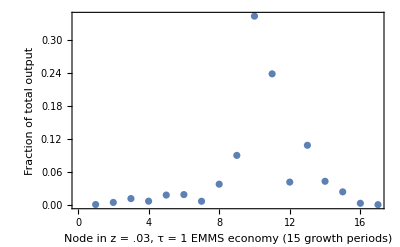

```mathematica
RV6=WorkingVols/Total[WorkingVols];
ListPlot[RV6, Frame->True,FrameLabel->{"Node in z = .03, τ = 1 EMMS economy (15 growth periods)","Fraction of total output"}]
```

We have arrived at the familiar picture compared to part (a).

(c) z = .1, τ = 2:

```mathematica
UpdateTopology[17,.1,2,emms,InitVolumesList]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.451156 | 0.431959 | 1.70747 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.38183 | 0.451156 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.120455 | 0 | 0 | 0
0 | 0.715542 | 0 | 0.494106 | 0 | 0 | 0 | 0 | 0.67466 | 0 | 0 | 0.245578 | 0.353553 | 0 | 0 | 0 | 0
0 | 0 | 1.70747 | 0 | 0.929429 | 0 | 0 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0 | 0.353553 | 0.252982 | 0.260766 | 0 | 0
0 | 0 | 0.286687 | 0 | 0 | 0.494106 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.494106 | 0 | 0.367238 | 4.82945 | 1.70747 | 0 | 0 | 2.15166 | 0.929429 | 0.810874 | 0 | 0.67466 | 0.414087 | 0 | 0 | 0
0 | 0 | 0.451156 | 0 | 1.90823 | 1 | 0 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0 | 0.810874 | 0 | 0
0 | 0 | 0 | 0 | 0.518206 | 0.38183 | 0 | 0.760726 | 1.17121 | 0 | 31.6228 | 0 | 8. | 1.5396 | 0 | 0 | 0
0 | 0 | 0.213434 | 0 | 0 | 0.328603 | 0 | 0.603682 | 0.866784 | 11.1803 | 0 | 0 | 0 | 1.90823 | 2.15166 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.17121 | 1.70747 | 0 | 1.27606 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0 | 0
0 | 0 | 0 | 0 | 0.245578 | 0.20249 | 0 | 0 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 0 | 0.19245 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.760726 | 0 | 1.17121 | 0.603682 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.1,2,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0 | 0
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0 | 0
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0
0 | 0 | 0 | 0 | 0.0534215 | 0.0496767 | 0 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Notably, Earth still doesn’t have any export relationships because of the high delta-v’s to its neighbors.

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.1,2,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.0341519 | 0.0199385 | 0.0206169 | 0.0240563 | 0.0203865 | 0.0172133 | 0.022095 | 0.0206169 | 0.0196131 | 0.0194011 | 0.018018 | 0.0190901 | 0.0181112 | 0.0182053 | 0.0149202 | 0
0.0965961 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0.0539949 | 0
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0393075 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0
0.0212121 | 0.0418199 | 0.0433783 | 0.0393075 | 0.0534215 | 0.0496767 | 0.037037 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The network is fully connected, except the Sun is excluded (which is theoretically sound).

```mathematica
EconomicGrowth[17,wtopm]
```

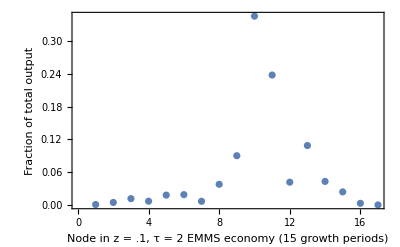

```mathematica
RV7=WorkingVols/Total[WorkingVols];
ListPlot[RV7, Frame->True,FrameLabel->{"Node in z = .1, τ = 2 EMMS economy (15 growth periods)","Fraction of total output"}]
```

(d) z = .03, τ = 2:

```mathematica
UpdateTopology[17,.03,2,emms,InitVolumesList]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.70747 | 0 | 0.603682 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.70747 | 0.67466 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.286687 | 1.70747 | 0 | 0 | 0 | 0 | 1.70747 | 0 | 0 | 0 | 0 | 0 | 0.252982 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4.82945 | 1.70747 | 0 | 0 | 0 | 0 | 0 | 0 | 0.67466 | 0 | 0 | 0 | 0
0 | 0.38183 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.31269 | 2.45164 | 0 | 1.70747 | 0 | 0.810874 | 0 | 0
0 | 0 | 0 | 0.178869 | 0.518206 | 0.38183 | 0 | 0 | 1.17121 | 0 | 31.6228 | 1.39754 | 0 | 1.5396 | 1.70747 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.268957 | 0 | 0.451156 | 0 | 0 | 6.08581 | 0 | 0 | 2.82843 | 3.31269 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1.39754 | 0 | 2.82843 | 0 | 1.07998 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.603682 | 0 | 0 | 1.17121 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

This network is initially very scarce.

```mathematica
WorkingVols=InitVolumesList;
```

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.03,2,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.120455 | 0 | 0.252982 | 0.129838 | 0 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0 | 0
0 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0
0 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0 | 0
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0 | 0
0 | 0 | 0.286687 | 0 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0
0 | 0 | 0 | 0 | 0.0534215 | 0 | 0 | 0.0576617 | 0 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

After 5 periods, the network is still missing quite a few relationships.

```mathematica
EconomicGrowth[17,wtopm]
```

```mathematica
UpdateTopology[17,.03,2,emms,WorkingVols]
```

```mathematica
MatrixForm[wtopm]
```

(0 | 0.0341519 | 0.0199385 | 0.0206169 | 0.0240563 | 0.0203865 | 0.0172133 | 0.022095 | 0.0206169 | 0.0196131 | 0.0194011 | 0.018018 | 0.0190901 | 0.0181112 | 0.0182053 | 0 | 0
0.0965961 | 0 | 0.120455 | 0.134997 | 0.252982 | 0.129838 | 0.0775275 | 0.174693 | 0.134997 | 0.114134 | 0.110221 | 0.0881177 | 0.104757 | 0.0894427 | 0.0908013 | 0.0539949 | 0
0.0563945 | 0.340698 | 0 | 0.451156 | 0.431959 | 1.70747 | 0.286687 | 0.603682 | 0.353553 | 0.260766 | 0.245578 | 0.170677 | 0.2254 | 0.174693 | 0.178869 | 0.0843325 | 0
0.0583133 | 0.38183 | 0.451156 | 0 | 0.494106 | 0.268957 | 0.125 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0680414 | 0.715542 | 0.166813 | 0.494106 | 0 | 0.603682 | 0.19245 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0534215 | 0.286687 | 1.70747 | 0.268957 | 0.929429 | 0 | 0.494106 | 1.70747 | 0.67466 | 0.431959 | 0.397413 | 0.245578 | 0.353553 | 0.252982 | 0.260766 | 0.104757 | 0
0.0393075 | 0.129838 | 0.286687 | 0.125 | 0.231809 | 0.494106 | 0 | 0.286687 | 0.20249 | 0.163092 | 0.156053 | 0.118285 | 0.146402 | 0.120455 | 0.122692 | 0.0663751 | 0
0.0624942 | 0.494106 | 0.603682 | 0.367238 | 4.82945 | 1.70747 | 0.286687 | 0 | 2.15166 | 0.929429 | 0.810874 | 0.397413 | 0.67466 | 0.414087 | 0.431959 | 0.134997 | 0
0.0583133 | 0.38183 | 0.451156 | 0.296296 | 1.90823 | 1 | 0.238528 | 6.08581 | 0 | 3.31269 | 2.45164 | 0.715542 | 1.70747 | 0.760726 | 0.810874 | 0.174693 | 0
0.0482036 | 0.213434 | 0.238528 | 0.178869 | 0.518206 | 0.38183 | 0.152721 | 0.760726 | 1.17121 | 0 | 31.6228 | 1.39754 | 8. | 1.5396 | 1.70747 | 0.219281 | 0
0.0463498 | 0.19245 | 0.213434 | 0.163092 | 0.431959 | 0.328603 | 0.140507 | 0.603682 | 0.866784 | 11.1803 | 0 | 1.70747 | 17.2133 | 1.90823 | 2.15166 | 0.231809 | 0
0.0407113 | 0.140507 | 0.152721 | 0.122692 | 0.260766 | 0.213434 | 0.108348 | 0.328603 | 0.414087 | 1.17121 | 1.70747 | 0 | 1.27606 | 0.637528 | 0.67466 | 0.163092 | 0
0.0437831 | 0.166813 | 0.183213 | 0.143404 | 0.340698 | 0.268957 | 0.125 | 0.451156 | 0.603682 | 2.82843 | 6.08581 | 1 | 0 | 2.82843 | 3.31269 | 0.252982 | 0
0.0399992 | 0.134997 | 0.146402 | 0.118285 | 0.245578 | 0.20249 | 0.104757 | 0.306454 | 0.38183 | 1 | 1.39754 | 0.544331 | 2.82843 | 0 | 1.07998 | 0.19245 | 0
0.0373478 | 0.116179 | 0.125 | 0.103035 | 0.197364 | 0.166813 | 0.0921947 | 0.238528 | 0.286687 | 0.603682 | 0.760726 | 0.38183 | 1.17121 | 0.603682 | 0 | 0.340698 | 0
0.0212121 | 0.0418199 | 0.0433783 | 0.0393075 | 0.0534215 | 0.0496767 | 0.037037 | 0.0576617 | 0.0617632 | 0.0775275 | 0.081957 | 0.0680414 | 0.0894427 | 0.0775275 | 0.120455 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0128793 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

After 10 periods, we have full connectivity except for Sun-related trade and Earth doesn’t export to Mars.

```mathematica
EconomicGrowth[17,wtopm]
```

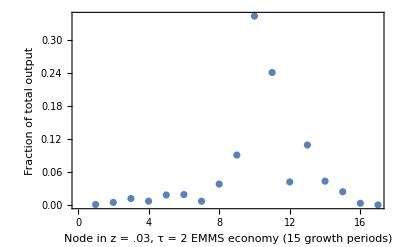

```mathematica
RV8=WorkingVols/Total[WorkingVols];
ListPlot[RV8, Frame->True,FrameLabel->{"Node in z = .03, τ = 2 EMMS economy (15 growth periods)","Fraction of total output"}]
```

It appears all parameter combinations result in the same weight structure regardless of some differences in network connectivity. We can plot all of the results together to visualize the overlap:

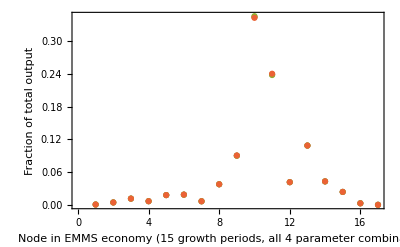

```mathematica
ListPlot[{RV5,RV6,RV7,RV8} ,Frame->True,FrameLabel->{"Node in EMMS economy (15 growth periods, all 4 parameter combinations)","Fraction of total output"}]
```